## Homeworld 1

## Exercise 1

```mathematica
(* Func draws from the uniform distribution on [a,b], using a standard uniform sample given by the function RandomReal[] *)
drawUniformNumber[a_, b_]  := a + (b-a) * RandomReal[];
```

```mathematica
(* Func draws n samples of U=(U1, U2) w/ U1~U[-1,1], U2~U[0,1] *)
drawTwoSamples[n_]  := Table[{drawUniformNumber[-1, 1], drawUniformNumber[0, 1]},{i,1,n}];
```

```mathematica
(* Computes numerically given sum of n summands *)
n = 100000;
U = drawTwoSamples[n];
 4/n Sum[If[U[[i]][[1]]^2 + U[[i]][[2]]^2 ≤ 1,1,0],{i,1,n}]
```

78477/25000

## Exercise 2

```mathematica
(* Func draws from the Weibull distr. w/ shape param. beta_ and scale param. 1 *)
drawWeibullNumber[beta_]:=(-Log[RandomReal[]])^(1/beta)
```

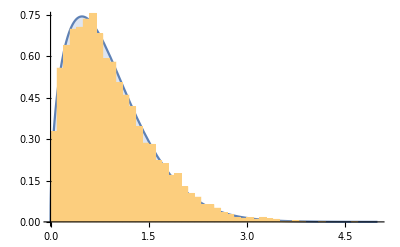

```mathematica
(* Plots a histogram of n simulated values of the Weibull distr. against the PDF of the Weibull distr. w/ shape param. beta *)
beta = 1.5;
n = 10000;
data=Table[drawWeibullNumber[beta],n];
Show[Plot[PDF[WeibullDistribution[beta, 1],x]//Evaluate,{x,0,5},Filling -> Axis],
Histogram[data,Automatic,"PDF"]]
```

## Exercise 4

```mathematica
(* Find maximum of func z(x) *)
z[x_]:= E/Sqrt[2 * Pi]*x^(-3/2)*Exp[-1/(2*x)];
c = Maximize[{z[x],x>0},x][[1]]
```

3 √(3/(2 ⅇ π))

```mathematica
(* Generates n samples from inverse Gaussian using A-R *)
f[x_] := z[x]Exp[-x/2];
g[x_]:= (1/2)*Exp[-x/2];

n=10000;
X={}; 

While[Length[X]<n,

(* samples from E(1/2) using Inversion *)
Y = -2*Log[RandomReal[]];
If[ RandomReal[]<=f[Y]/(2*c*g[Y]),AppendTo[X, Y]; ] ;
];
```

```mathematica
(* Constructs confidence intervals *)
XSquared = X^2;
meanX = Mean[X];
meanXSquared = Mean[XSquared];
varX = Variance[X];
varXSquared = Variance[XSquared];
Print["Sample mean of X is: ",meanX]
Print["Sample mean of X^2 is: ",meanXSquared]
Print["(Unbiased) sample variance of X is: ",varX]
Print["(Unbiased) sample variance of X^2 is: ",varXSquared]
```

Sample mean of X is: 0.995353

Sample mean of X^2 is: 1.98367

(Unbiased) sample variance of X is: 0.993044

(Unbiased) sample variance of X^2 is: 33.8872

```mathematica
(* Confidence interval for EX^2 *)
criticalTValue=Quantile[StudentTDistribution[n-1],0.975];
meanXSquared-criticalTValue*varXSquared/Sqrt[n]
meanXSquared+criticalTValue*varXSquared/Sqrt[n]
```

1.31942

2.64793

```mathematica
(* Confidence interval for VarX *)
```

```mathematica
criticalChiSquaredValueLower=Quantile[ChiSquareDistribution[n-1],0.025];
criticalChiSquaredValueUpper=Quantile[ChiSquareDistribution[n-1],0.975];
varX * (n-1)/criticalChiSquaredValueUpper
varX * (n-1)/criticalChiSquaredValueLower
```

0.966082

1.02116